## Generalized Model Analysis of the SH0ES Measurement of H_0. Search for a transition is implemented. For different generalized parameters, the parameter ‘col’ needs to be changed and the table qpar1. The rest may even remain as they are (the range of the final plot may also need to be changed).

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
Off[Inverse::luc];
```

## Matrix of Measurements Y- Matrix of Parameters q - Design Matrix L- Error Matrix C

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
distc=Import[".\\data\\distc.txt","Table"];
dist1=distc[[All,1]];
dof=3446;
NN=3492;
MM=48;
maxdist=60; (* this is the maximum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
mindist=1; (* this is the minimum distance considered in do loop in Mpc that distinguishes nearby and distant objects/constraints in Y.  *)
step=2; (* this is the distance step considered in do loop  *)

col=47-5; (* this column corresponds to the parameter to be split (e.g. for Subscript[b, W] period luminosity slope we have col=42) *)
qpar1={μ67,μ385,μ354,μ356,μ738,μ294,μ228,μ163,μ193,μ201,μ272,μ354,μ266,μ425,μ244,μ24,μ208,μ344,μ151,μ190,μ293,μ164,μ319,μ198,μ421,μ463,μ280,μ207,μ449,μ303,μ310,μ128,μ468,μ344,μ466,μ605,μ294,ΔμΝ4258,MW,ΔμLMC,μM31,bWs,bWl,MB,ZW,X,ΔZp,p5ogh0}; (* introduce here the names of the two new parameters that replace the previous parameter *)

Call=cdata[[1]]//Normal; (* Covariance matrix. This does not change since the Y matrix remained the same with no new constraints. *)
InvCall=Inverse[Call];
it=InvCall.Call//Chop;
zerot=it-IdentityMatrix[Length[it]]//Chop;
zerot[[1]];  (* test the inversion of Call due to the mathematica complaints. These are due to the parameter X introduced arbitrarily in the SH0ES data analysis and not shown in https://arxiv.org/pdf/2112.04510.pdf  (Riess21). This leads to Call with a column and raw that are 0 except of the diagonal point which is 10^-9. This raw and column of Call creates the complaints but the end inversion is fine. *)
Y=ydata;
trL=ldata[[1]]//Normal;
L=Transpose[trL]; (* Y = L.qpar . L denotes the original model used by the SH0ES team which will be generalized here. *)
```

## Search for a transition (b_W) - Results - Figure 9

```mathematica
percol1=L[[All,col]]//Normal; (* construct two columns from the period (Subscript[b, W]) column of L with nearby and distant objects *)
```

Distance=1---------------

H_0=74.5921±1.25627

bWs=-0.0275019±0.0162464

bWl=0.0601854±0.0370943

σ-distance = 2.16533

Mb=-19.2074±0.0357064

Mw=-5.89785±0.0181625

Zw=-0.222854±0.0453006

χ_min^2 = 3548.05

χ_red^2 = 1.02961

AIC = 3644.05

ΔAIC = -2.71002

BIC = 3939.64

ΔBIC = 3.44821

Distance=3---------------

H_0=74.5921±1.25627

bWs=-0.0275019±0.0162464

bWl=0.0601854±0.0370943

σ-distance = 2.16533

Mb=-19.2074±0.0357064

Mw=-5.89785±0.0181625

Zw=-0.222854±0.0453006

χ_min^2 = 3548.05

χ_red^2 = 1.02961

AIC = 3644.05

ΔAIC = -2.71002

BIC = 3939.64

ΔBIC = 3.44821

Distance=5---------------

H_0=74.5921±1.25627

bWs=-0.0275019±0.0162464

bWl=0.0601854±0.0370943

σ-distance = 2.16533

Mb=-19.2074±0.0357064

Mw=-5.89785±0.0181625

Zw=-0.222854±0.0453006

χ_min^2 = 3548.05

χ_red^2 = 1.02961

AIC = 3644.05

ΔAIC = -2.71002

BIC = 3939.64

ΔBIC = 3.44821

Distance=7---------------

H_0=73.9959±1.23799

bWs=-0.021964±0.0161406

bWl=0.0330683±0.037179

σ-distance = 1.35777

Mb=-19.2248±0.035448

Mw=-5.8962±0.0181586

Zw=-0.22002±0.0452781

χ_min^2 = 3550.89

χ_red^2 = 1.03044

AIC = 3646.89

ΔAIC = 0.128258

BIC = 3942.48

ΔBIC = 6.28649

Distance=9---------------

H_0=74.7418±1.50137

bWs=-0.0204014±0.015542

bWl=0.0607692±0.0494996

σ-distance = 1.56452

Mb=-19.2031±0.0428589

Mw=-5.89315±0.0180545

Zw=-0.218416±0.0452234

χ_min^2 = 3550.28

χ_red^2 = 1.03026

AIC = 3646.28

ΔAIC = -0.477635

BIC = 3941.88

ΔBIC = 5.6806

Distance=11---------------

H_0=74.7418±1.50137

bWs=-0.0204014±0.015542

bWl=0.0607692±0.0494996

σ-distance = 1.56452

Mb=-19.2031±0.0428589

Mw=-5.89315±0.0180545

Zw=-0.218416±0.0452234

χ_min^2 = 3550.28

χ_red^2 = 1.03026

AIC = 3646.28

ΔAIC = -0.477635

BIC = 3941.88

ΔBIC = 5.6806

Distance=13---------------

H_0=74.4233±1.48494

bWs=-0.0190763±0.0155163

bWl=0.0476228±0.0494055

σ-distance = 1.28801

Mb=-19.2124±0.0425597

Mw=-5.89326±0.018054

Zw=-0.218343±0.0452287

χ_min^2 = 3551.07

χ_red^2 = 1.03049

AIC = 3647.07

ΔAIC = 0.314602

BIC = 3942.67

ΔBIC = 6.47283

Distance=15---------------

H_0=74.4233±1.48494

bWs=-0.0190763±0.0155163

bWl=0.0476228±0.0494055

σ-distance = 1.28801

Mb=-19.2124±0.0425597

Mw=-5.89326±0.018054

Zw=-0.218343±0.0452287

χ_min^2 = 3551.07

χ_red^2 = 1.03049

AIC = 3647.07

ΔAIC = 0.314602

BIC = 3942.67

ΔBIC = 6.47283

Distance=17---------------

H_0=74.5859±1.44822

bWs=-0.0189053±0.0153248

bWl=0.0594739±0.0500123

σ-distance = 1.49843

Mb=-19.2077±0.0413237

Mw=-5.89323±0.018054

Zw=-0.217979±0.0452176

χ_min^2 = 3550.42

χ_red^2 = 1.0303

AIC = 3646.42

ΔAIC = -0.338426

BIC = 3942.02

ΔBIC = 5.8198

Distance=19---------------

H_0=74.5859±1.44822

bWs=-0.0189053±0.0153248

bWl=0.0594739±0.0500123

σ-distance = 1.49843

Mb=-19.2077±0.0413237

Mw=-5.89323±0.018054

Zw=-0.217979±0.0452176

χ_min^2 = 3550.42

χ_red^2 = 1.0303

AIC = 3646.42

ΔAIC = -0.338426

BIC = 3942.02

ΔBIC = 5.8198

Distance=21---------------

H_0=72.7994±1.21746

bWs=-0.0128311±0.0150442

bWl=-0.0298637±0.0486625

σ-distance = 0.334398

Mb=-19.2601±0.0354276

Mw=-5.89361±0.0180547

Zw=-0.216787±0.0452121

χ_min^2 = 3552.63

χ_red^2 = 1.03094

AIC = 3648.63

ΔAIC = 1.87558

BIC = 3944.23

ΔBIC = 8.03381

Distance=23---------------

H_0=72.4274±1.18707

bWs=-0.0116853±0.0150391

bWl=-0.0572522±0.0481562

σ-distance = 0.903212

Mb=-19.2713±0.034716

Mw=-5.89372±0.0180541

Zw=-0.21679±0.0452089

χ_min^2 = 3551.85

χ_red^2 = 1.03072

AIC = 3647.85

ΔAIC = 1.08797

BIC = 3943.44

ΔBIC = 7.2462

Distance=25---------------

H_0=72.908±1.14735

bWs=-0.0131373±0.0149997

bWl=-0.024937±0.0491619

σ-distance = 0.229569

Mb=-19.2569±0.0332625

Mw=-5.89353±0.018053

Zw=-0.216393±0.0452153

χ_min^2 = 3552.7

χ_red^2 = 1.03096

AIC = 3648.7

ΔAIC = 1.94065

BIC = 3944.3

ΔBIC = 8.09888

Distance=27---------------

H_0=72.8709±1.14179

bWs=-0.0130179±0.0150008

bWl=-0.0283215±0.0490605

σ-distance = 0.2983

Mb=-19.258±0.0331101

Mw=-5.89354±0.018053

Zw=-0.216376±0.0452132

χ_min^2 = 3552.66

χ_red^2 = 1.03095

AIC = 3648.66

ΔAIC = 1.89977

BIC = 3944.25

ΔBIC = 8.058

Distance=29---------------

H_0=73.3074±1.11988

bWs=-0.0142269±0.0149699

bWl=0.0137747±0.0518435

σ-distance = 0.518918

Mb=-19.245±0.0322543

Mw=-5.89348±0.0180531

Zw=-0.216715±0.045209

χ_min^2 = 3552.46

χ_red^2 = 1.03089

AIC = 3648.46

ΔAIC = 1.69771

BIC = 3944.05

ΔBIC = 7.85594

Distance=31---------------

H_0=72.8554±1.07081

bWs=-0.01299±0.0149528

bWl=-0.0409606±0.0563615

σ-distance = 0.479678

Mb=-19.2585±0.0309228

Mw=-5.89352±0.0180529

Zw=-0.216211±0.0452145

χ_min^2 = 3552.5

χ_red^2 = 1.03091

AIC = 3648.5

ΔAIC = 1.7452

BIC = 3944.1

ΔBIC = 7.90343

Distance=33---------------

H_0=72.815±1.06363

bWs=-0.0129911±0.014938

bWl=-0.0511961±0.0600296

σ-distance = 0.6176

Mb=-19.2597±0.0307229

Mw=-5.89346±0.0180532

Zw=-0.215773±0.0452258

χ_min^2 = 3552.34

χ_red^2 = 1.03086

AIC = 3648.34

ΔAIC = 1.58027

BIC = 3943.93

ΔBIC = 7.7385

Distance=35---------------

H_0=72.752±1.04844

bWs=-0.0128678±0.0149312

bWl=-0.0732819±0.064511

σ-distance = 0.912374

Mb=-19.2616±0.0303024

Mw=-5.89339±0.0180535

Zw=-0.215137±0.045234

χ_min^2 = 3551.85

χ_red^2 = 1.03072

AIC = 3647.85

ΔAIC = 1.09349

BIC = 3943.45

ΔBIC = 7.25172

Distance=37---------------

H_0=72.923±1.03809

bWs=-0.0132836±0.0149243

bWl=-0.046986±0.0736585

σ-distance = 0.448436

Mb=-19.2565±0.0299061

Mw=-5.89349±0.0180531

Zw=-0.216153±0.045218

χ_min^2 = 3552.54

χ_red^2 = 1.03092

AIC = 3648.54

ΔAIC = 1.78481

BIC = 3944.14

ΔBIC = 7.94304

Distance=39---------------

H_0=72.9398±1.03296

bWs=-0.0133114±0.0149233

bWl=-0.0464665±0.0768855

σ-distance = 0.423327

Mb=-19.256±0.0297466

Mw=-5.89347±0.0180533

Zw=-0.216032±0.0452262

χ_min^2 = 3552.57

χ_red^2 = 1.03093

AIC = 3648.57

ΔAIC = 1.80925

BIC = 3944.16

ΔBIC = 7.96748

Distance=41---------------

H_0=72.9398±1.03296

bWs=-0.0133114±0.0149233

bWl=-0.0464665±0.0768855

σ-distance = 0.423327

Mb=-19.256±0.0297466

Mw=-5.89347±0.0180533

Zw=-0.216032±0.0452262

χ_min^2 = 3552.57

χ_red^2 = 1.03093

AIC = 3648.57

ΔAIC = 1.80925

BIC = 3944.16

ΔBIC = 7.96748

Distance=43---------------

H_0=73.0094±1.03057

bWs=-0.0134538±0.0149226

bWl=-0.0256382±0.0814105

σ-distance = 0.147212

Mb=-19.2539±0.0296359

Mw=-5.89351±0.018053

Zw=-0.216463±0.0452156

χ_min^2 = 3552.74

χ_red^2 = 1.03097

AIC = 3648.74

ΔAIC = 1.9771

BIC = 3944.33

ΔBIC = 8.13533

Distance=45---------------

H_0=72.9807±1.0287

bWs=-0.013382±0.0149233

bWl=-0.0372934±0.0830607

σ-distance = 0.283341

Mb=-19.2548±0.0295929

Mw=-5.89352±0.0180529

Zw=-0.216427±0.0452117

χ_min^2 = 3552.67

χ_red^2 = 1.03096

AIC = 3648.67

ΔAIC = 1.91539

BIC = 3944.27

ΔBIC = 8.07362

Distance=47---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=49---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=51---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=53---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=55---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=57---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

Distance=59---------------

H_0=73.1729±1.01337

bWs=-0.0133954±0.0149156

bWl=0.315086±0.239154

σ-distance = 1.37085

Mb=-19.2492±0.0290256

Mw=-5.89365±0.0180532

Zw=-0.217438±0.0452127

χ_min^2 = 3550.86

χ_red^2 = 1.03043

AIC = 3646.86

ΔAIC = 0.104606

BIC = 3942.46

ΔBIC = 6.26284

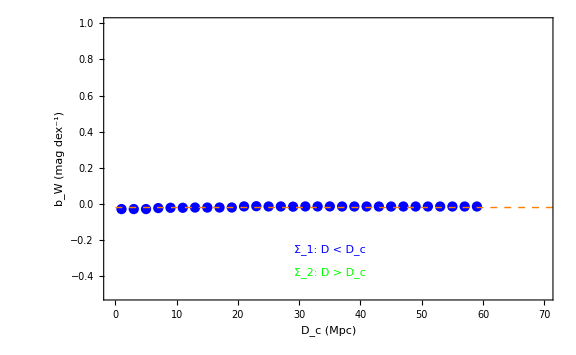
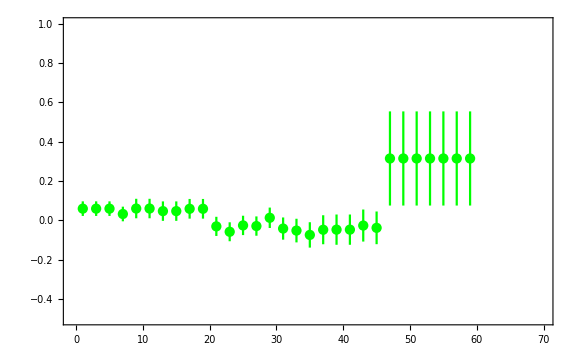
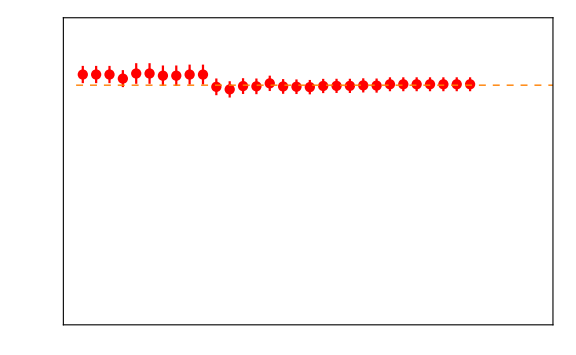

```mathematica
plh0dat={};
plparsdat={};
plparldat={};
plsdist={};
plchi2min={};
plchi2red={};
plaic={};
pldaic={};
plbic={};
pldbic={};
Do[
percol1s=percol1;
percol1l=percol1;
Do[
If[dist1[[i]]≥ dcrit,percol1s[[i]]=0]; (* in the nearby Subscript[b, W,s] column put 0 in the distant elements i.e. those that are beyond dcrit *)
If[0<=dist1[[i]]< dcrit,percol1l[[i]]=0] (* in the distant Subscript[b, W,l] column put 0 in the nearby elements i.e. those that are closer than dcrit. Elements with negative distance are ignored. *)
,{i,1,Length[dist1]}];
trL1=Drop[trL,{col}] ;(* Remove the bW column of L to replace it with two other columns for the nearby and distant parameters (Subscript[b, W,s] and Subscript[b, W,l]) *)
trL2=Insert[Insert[trL1,percol1s,col],percol1l,col+1] ;(* Replace with the new columns *)
Lnew=Transpose[trL2]; (* this is the model matrix Lnew for the new model with one new parameter *)
trLnew=trL2 ;(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *);
sigma=Inverse[trLnew.InvCall.Lnew];
qbf=sigma.(trLnew.InvCall.Y) ;(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf Eq. 11 *);
(* the best fit papameter values with 1 sigma errors for Subscript[H, 0] and for the two new parameters *)
h0=10^(qbf[[48]]/5) (* We obtain the correct value of h0 since qbf[[47]]= 5 log Subscript[H, 0] *);
dqbf48=Sqrt[sigma[[48,48]]];
dh0=Log[10] h0 dqbf48/5 ;
vec=Y-Lnew.qbf;
chi2min=vec.InvCall.vec;
Print["Distance=",dcrit,"---------------"];
Print["H_0=",h0,"±",dh0];
dpars=Sqrt[sigma[[col,col]]];
dparl=Sqrt[sigma[[col+1,col+1]]];
pars=ToString[qpar1[[col]]];
parl=ToString[qpar1[[col+1]]];
sdist=Abs[(qbf[[col]] -qbf[[col+1]])]/(dpars ^2+dparl ^2)^0.5 (* We obtain the σ-distance *);
Print[pars,"=",qbf[[col]],"±",dpars];
Print[parl,"=",qbf[[col+1]],"±",dparl];
Print["σ-distance = ",sdist];
Print["Mb","=",qbf[[44]],"±",Sqrt[sigma[[44,44]]]];
Print["Mw","=",qbf[[39]],"±",Sqrt[sigma[[39,39]]]];
Print["Zw","=",qbf[[45]],"±",Sqrt[sigma[[45,45]]]];
Print["χ_min^2 = ",chi2min];
Print["χ_red^2 = ",chi2min/dof];
Print["AIC = ",chi2min+2*MM];
Print["ΔAIC = ",chi2min+2*MM-3646.7593303](* this is the AIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
Print["BIC = ",chi2min+MM*Log[NN]];
Print["ΔBIC = ",chi2min+MM*Log[NN]-3936.1961364](* this is the BIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
AppendTo[plh0dat,{dcrit,h0,dh0}];
AppendTo[plparsdat,{dcrit,qbf[[col]],dpars}];
AppendTo[plparldat,{dcrit,qbf[[col+1]],dparl}];
AppendTo[plsdist,{dcrit,sdist}];
AppendTo[plchi2min,{dcrit,chi2min}];
AppendTo[plchi2red,{dcrit,chi2min/dof}];
AppendTo[plaic,{dcrit,chi2min+2*MM}];
AppendTo[pldaic,{dcrit,chi2min+2*MM-3646.7593303}](* this is the AIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
AppendTo[plbic,{dcrit,chi2min+MM*Log[NN]}];
AppendTo[pldbic,{dcrit,chi2min+MM*Log[NN]-3936.1961364}](* this is the BIC obtained from the zero order model of SH0ES (see Baseline1 file)*);
chi2min0=3552.76 (* this is the Subscript[χ, min]^2 obtained from the zero order model of SH0ES (see Baseline1 file)*);
deltachi2min=chi2min-chi2min0  (* this is the improvement of chi2min obtained by the introduction of the new parameter *),{dcrit,mindist,maxdist,step}]
data1=plparsdat;
data2=plparldat;
data3=plh0dat;
plot1=ErrorListPlot[data1,PlotRange->{{-0.5,70},{-0.5,1}},PlotStyle->Blue,ImagePadding->70,Axes->False,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],FrameLabel->{"D_c (Mpc)","b_W (mag dex^-1)"},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,-0.019},{80,-0.019}}]},{Blue,Inset["Σ_1: D < D_c",{35,-0.25}]},{Green,Inset["Σ_2: D > D_c",{35,-0.38}]}}];
plot2=ErrorListPlot[data2,PlotRange->{{-0.5,70},{-0.5,1}},PlotStyle->Green,ImagePadding->70,Axes->False,Frame->{{True,False},{True,True}},FrameStyle->Directive[{{Blue,Automatic},{Blue,Blue}},Thick],BaseStyle->{Large,FontFamily->"Times",18}];
plot3=ErrorListPlot[data3,PlotRange->{{-0.5,70},{39,82}},PlotStyle->Red,ImagePadding->70,Axes->False,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},Thick],FrameLabel->{{None,"H_0 (km sec^-1 Mpc^-1)"},{None,None}},BaseStyle->{Large,FontFamily->"Times",18},Epilog->{Dashing[{Small,Small}],Thickness[Medium],Orange,Line[{{0,73.04},{80,73.04}}]}];
figbw=Overlay[Show[#,ImageSize->Large]&/@{plot1,plot2,plot3}]
```

```mathematica
Export[NotebookDirectory[]<>"figbw.pdf",figbw,ImageResolution->1000];
```

## Figures 12, 13 (Magenta curves)

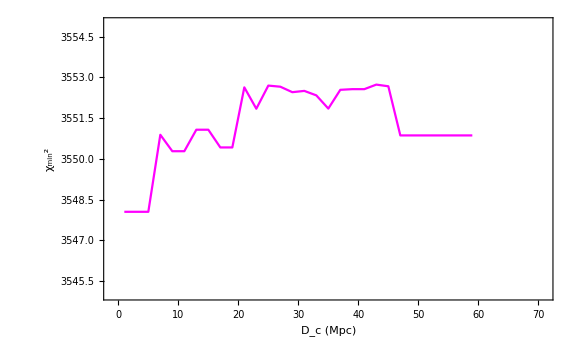

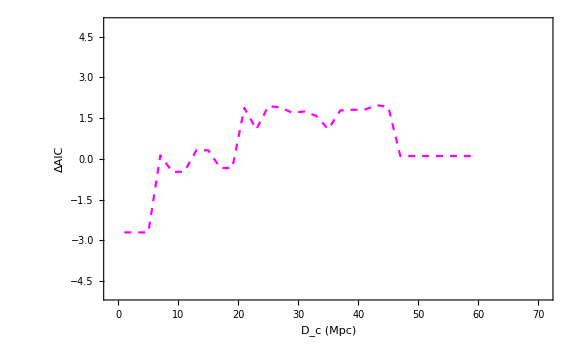

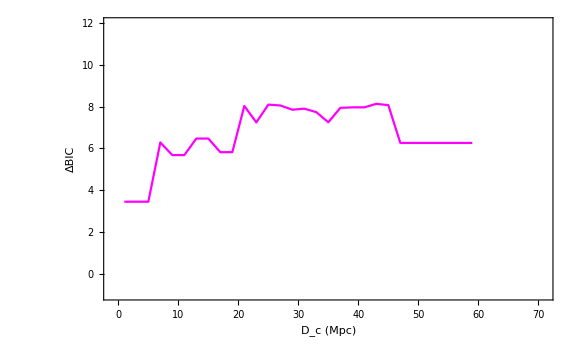

```mathematica
figsdbw=ListPlot[plsdist,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (b_W)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,4}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the σ-distance  plot obtained from the transition model Subscript[b, W] *);
figchibw=ListPlot[plchi2min,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_min^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3545,3555}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, min]^2  plot obtained from the transition model Subscript[b, W] *)
figchiredbw=ListPlot[plchi2red,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","χ_red^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{1.0285,1.032}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the Subscript[χ, red]^2  plot obtained from the transition model Subscript[b, W] *);
figaicbw=ListPlot[plaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","AIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3642,3651}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the AIC  plot obtained from the transition model Subscript[b, W] *);
figdaicbw=ListPlot[pldaic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔAIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-5,5}},Axes->False,PlotStyle->{Dashed,Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔAIC  plot obtained from the transition model Subscript[b, W] *)
figbicbw=ListPlot[plbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","BIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{3938,3951}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the BIC  plot obtained from the transition model Subscript[b, W] *);
figdbicbw=ListPlot[pldbic,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","ΔBIC"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-1,12}},Axes->False,PlotStyle->{Magenta},ImageSize->Large, FrameStyle -> Directive[Black, Thick]](*this is the ΔBIC  plot obtained from the transition model Subscript[b, W] *)
```